# Figures for DG notes

Spring 2025

```mathematica
Needs["MaTeX`"];
SetOptions[MaTeX,"BasePreamble"->{"\\usepackage{newtx,exscale}"},FontSize->16];
```

```mathematica
ColorMapSuitePath=NotebookDirectory[]<>"/ScientificColourMaps7";
ColorMapSuite[name_String]:=ColorMapSuite[name,-1]
ColorMapSuite[name_String,el_]:=With[{list=Transpose@{Subdivide[0,1,255],RGBColor@@@First@Import[ColorMapSuitePath<>"/"<>name<>"/"<>name<>".mat"]}},Blend[list,{##}[[el]]]&]
ColorMapSuiteCategorical[name_String]:=RGBColor@@@First@Import[ColorMapSuitePath<>"/"<>name<>"/CategoricalPalettes/"<>name<>"S.mat"];
ColorMapSuiteDiscrete[name_String,n_]:=RGBColor@@@First@Import[ColorMapSuitePath<>"/"<>name<>"/DiscretePalettes/"<>name<>IntegerString[n]<>".mat"];
cols=ColorMapSuiteCategorical["batlow"];
```

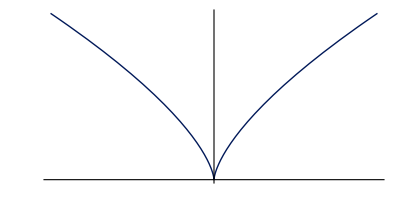

```mathematica
cusp=ParametricPlot[{t^3,t^2}, {t,-1,1},PlotStyle->{cols[[1]],Thick},Ticks->{Table[{i,MaTeX[i]},{i,-1,1}],Table[{i,MaTeX[i]},{i,0,1}]}]
```

```mathematica
Export[NotebookDirectory[]<>"cusp.pdf",cusp]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/cusp.pdf

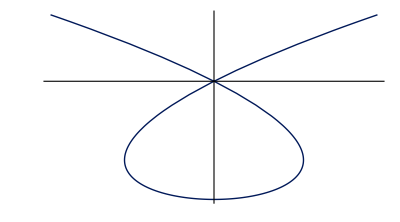

```mathematica
α[t_]:={t^3-4t,t^2-4};
conic=ParametricPlot[α[t], {t,-2.5,2.5},PlotStyle->{cols[[1]],Thick},Ticks->{Table[{i,MaTeX[i]},{i,-6,6,2}],Table[{i,MaTeX[i]},{i,-4,2,2}]}]
```

```mathematica
Export[NotebookDirectory[]<>"conic.pdf",conic]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/conic.pdf

```mathematica
D[{√(1-z^2)Cos[θ],√(1-z^2)Sin[θ],z},θ]
```

{-√(1-z^2) Sin[θ],√(1-z^2) Cos[θ],0}

```mathematica
D[{√(1-z^2)Cos[θ],√(1-z^2)Sin[θ],z},z]
```

{-(z Cos[θ])/(√(1-z^2)),-(z Sin[θ])/(√(1-z^2)),1}

```mathematica
dtheta=With[{zstep=.1,θstep=2π/15},
Graphics3D[{cols[[5]],Arrowheads[.02],Table[Arrow[Tube[{#,#+.35Sqrt[1-z^2]{-Sin[θ],Cos[θ],0}},.006]]&[{Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z}],{z,-1+zstep,1-zstep,zstep},{θ,0,2π-θstep,θstep}],White,Opacity[.7],Sphere[]},PlotRange->1.4,ImageSize->800,Lighting->"Neutral",Boxed->False,ViewPoint->{10,0,3},ViewVertical->{0,0,1},SphericalRegion->False,ViewAngle->π/37]
];
```

```mathematica
dtheta
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"dtheta.png",dtheta,Background->None]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/dtheta.png

```mathematica
dz=With[{zstep=.2,θstep=2π/15},
Graphics3D[{cols[[3]],Arrowheads[.02],Table[Arrow[Tube[{#,#+.35{-(z Cos[θ])/(√(1-z^2)),-(z Sin[θ])/(√(1-z^2)),1}},.006]]&[{Sqrt[1-z^2]Cos[θ],Sqrt[1-z^2]Sin[θ],z}],{z,-1+zstep,1-zstep,zstep},{θ,0,2π-θstep,θstep}],White,Opacity[.7],Sphere[]},PlotRange->1.4,ImageSize->800,Lighting->"Neutral",Boxed->False,ViewPoint->{10,0,3},ViewVertical->{0,0,1},SphericalRegion->False,ViewAngle->π/37]
];
```

```mathematica
dz
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"dz.png",dz,Background->None]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/dz.png

```mathematica
X[{x_,y_,z_}]:={z x, z y, z^2-1};
```

```mathematica
flowfield=Module[{n=4,m=12,x,y,z},
Graphics3D[{cols[[5]],Thickness[.007],
Table[{x,y,z}={√(1-z^2)Cos[θ+(-1)^(n z)#/n],√(1-z^2)Sin[θ+(-1)^(n z)#/n],z};
Arrow[Tube[{{x,y,z},{x,y,z}+X[{x,y,z}]}]],
{z,-1,1,1/n},{θ,0,2π-#,#}]&[2π/m],
Opacity[.6],White,Sphere[]
},
Boxed->False,ViewPoint->Front,Lighting->"Neutral",ImageSize->800]
]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"flowfield.png",flowfield,Background->None]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/flowfield.png

```mathematica
{Subscript[ϕ, 1][t],Subscript[ϕ, 2][t],Subscript[ϕ, 3][t]}/.DSolve[Table[Subscript[ϕ, i]'[t]==X[{Subscript[ϕ, 1][t],Subscript[ϕ, 2][t],Subscript[ϕ, 3][t]}][[i]],{i,1,3}]&&Subscript[ϕ, 1][0]==x&&Subscript[ϕ, 2][0]==y&&Subscript[ϕ, 3][0]==z,{Subscript[ϕ, 1],Subscript[ϕ, 2],Subscript[ϕ, 3]},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{-(2 ⅇ^t x)/(-1-ⅇ^(2 t)-z+ⅇ^(2 t) z),-(2 ⅇ^t y)/(-1-ⅇ^(2 t)-z+ⅇ^(2 t) z),-(1-ⅇ^(2 t)+z+ⅇ^(2 t) z)/(-1-ⅇ^(2 t)-z+ⅇ^(2 t) z)}}

```mathematica
conformalflow=Module[{n=4,m=12,x,y,z},
Show[
Graphics3D[{cols[[5]],Thickness[.007],
Table[{x,y,z}={√(1-z^2)Cos[θ+(-1)^(n z)#/n],√(1-z^2)Sin[θ+(-1)^(n z)#/n],z};
Arrow[Tube[{{x,y,z},{x,y,z}+X[{x,y,z}]}]],
{z,-1,1,1/n},{θ,0,2π-#,#}]&[2π/m],
Opacity[.6],White,Sphere[]
}],
With[{z=0,x=Cos[θ],y=Sin[θ]},
ParametricPlot3D[Table[{-(2 ⅇ^t x)/(-1-ⅇ^(2 t)-z+ⅇ^(2 t) z),-(2 ⅇ^t y)/(-1-ⅇ^(2 t)-z+ⅇ^(2 t) z),-(1-ⅇ^(2 t)+z+ⅇ^(2 t) z)/(-1-ⅇ^(2 t)-z+ⅇ^(2 t) z)},{θ,2 π/(m n),2π-π/m,π/m}],{t,-10,10},PlotStyle->Directive[Thickness[.007],cols[[3]]]]],
Boxed->False,ViewPoint->Front,ViewVertical->{0,0,1},Lighting->"Neutral",ImageSize->800]
]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"conformalflow.png",conformalflow,Background->None]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/conformalflow.png

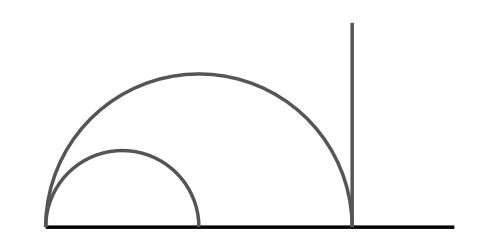

```mathematica
hyperbolicgeodesics=Graphics[{Black,Thickness[.005],Line[{{-1,0},{1,0}}],Darker[Gray],Line[{{1/2,0},{1/2,1}}],Circle[{-5/8,0},3/8,{0,π}],Circle[{-1/4,0},3/4,{0,π}]},ImageSize->500]
```

```mathematica
Export[NotebookDirectory[]<>"hyperbolicgeodesics.pdf",hyperbolicgeodesics]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/hyperbolicgeodesics.pdf

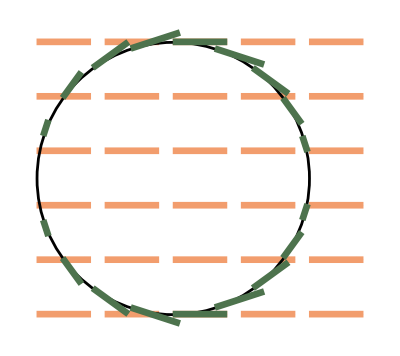

```mathematica
pullbackdx=Graphics[{Thickness[.012],cols[[5]],Table[Arrow[{#,#+.4{1,0}}]&[{x,y}],{y,-1,1,.4},{x,-1,1,.5}],Thickness[.005],Black,Circle[],Thickness[.012],cols[[7]],Table[Arrow[{#,#-.4#[[2]]{-#[[2]],#[[1]]}}]&[ReIm[E^(I θ)]],{θ,0,2π,2π/20}]}]
```

```mathematica
Export[NotebookDirectory[]<>"pullbackdx.pdf",pullbackdx]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/pullbackdx.pdf

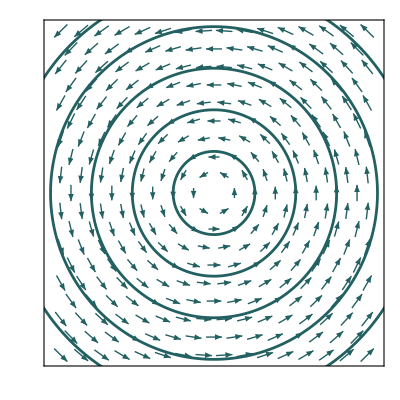

```mathematica
rotationfield=Show[VectorPlot[{-v,u},{u,-2,2},{v,-2,2},VectorScaling->Automatic,VectorColorFunction->None,VectorStyle->cols[[4]],FrameTicks->None],ParametricPlot[Table[r{Cos[θ],Sin[θ]},{r,0,3,.5}],{θ,0,2π},PlotStyle->cols[[4]]]]
```

```mathematica
Export[NotebookDirectory[]<>"rotationfield.pdf",rotationfield]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/rotationfield.pdf

```mathematica
circs=Graphics[Table[Circle[{0,0},r],{r,0,1,1/20}]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"circs.pdf",circs]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/circs.pdf

```mathematica
planes=Graphics3D[{cols[[3]],Opacity[.7],EdgeForm[{Thick,Darker[cols[[3]]]}],Table[InfinitePlane[{0,0,z}+#&/@{{0,0,0},{1,0,0},{0,1,0}}],{z,-1,1,1/4}]},Lighting->"Neutral",Boxed->False,ImageSize->500]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"planes.png",planes]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/planes.png

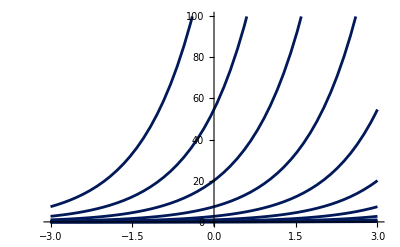

```mathematica
Plot[Table[E^(r+c),{c,-5,5}],{r,-3,3},Ticks->None,PlotStyle->cols[[1]]]
```

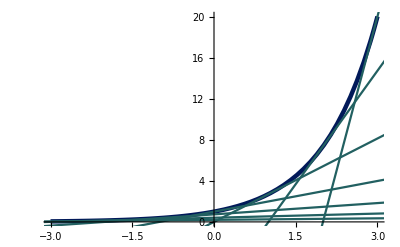

```mathematica
expgraph=Show[
Plot[ E^r,{r,-3,3},PlotStyle->Directive[Thickness[.008],cols[[1]]],Ticks->None],
Graphics[{cols[[4]],Thickness[.004],Table[InfiniteLine[{{r,E^r},{r,E^r}+{1,E^r}}],{r,-3,3}]}]
]
```

```mathematica
Export[NotebookDirectory[]<>"expgraph.pdf",expgraph]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/expgraph.pdf

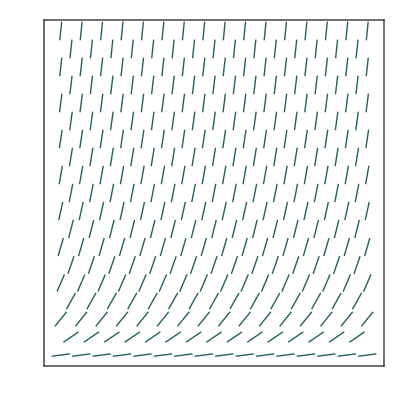

```mathematica
VectorPlot[{1,y},{x,-5,5},{y,0,10},VectorMarkers->"Segment",VectorColorFunction->None,VectorStyle->cols[[4]],FrameTicks->None]
```

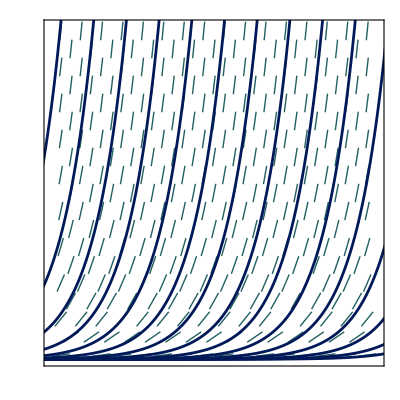

```mathematica
expgraphfield=Show[VectorPlot[{1,y},{x,-5,5},{y,0,10},VectorMarkers->"Segment",VectorColorFunction->None,VectorStyle->cols[[4]],FrameTicks->None],Plot[Table[E^(r+c),{c,-7,7}],{r,-6,6},PlotRange->All,PlotStyle->cols[[1]]]]
```

```mathematica
Export[NotebookDirectory[]<>"expgraphfield.pdf",expgraphfield]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/expgraphfield.pdf

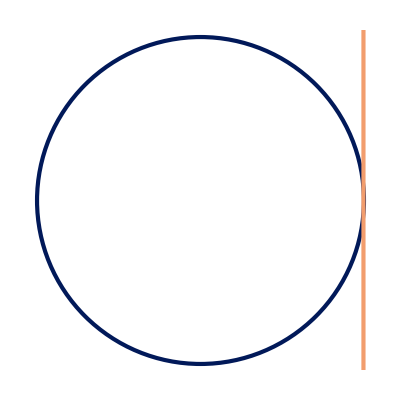

```mathematica
circletangent=Graphics[{cols[[1]],Thickness[.0075],Circle[],cols[[5]],InfiniteLine[{{1,0},{1,1}}]}]
```

```mathematica
Export[NotebookDirectory[]<>"circletangent.pdf",circletangent]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/circletangent.pdf

```mathematica
smootheststep[t_]:=-20t^7+70t^6-84t^5+35t^4;
wrap[s_,t_]:=If[t<s,E^(I t),E^(I s)+I E^(I s)(t-s)];
```

```mathematica
DynamicModule[{u},
Animate[
u=π s;
Show[Graphics[{cols[[1]],Thickness[.0075],Circle[]}],
ParametricPlot[{ReIm[wrap[u,t]],ReIm[Conjugate[wrap[u,t]]]},{t,0,π},PlotStyle->Directive[Thickness[.0075],cols[[5]],CapForm["Round"]]],PlotRange->1.5,Axes->False,ImageSize->540],
{s,0,1}]
]
```

```mathematica
wrapfig=Module[{u},Table[
u=π s;
Show[Graphics[{cols[[1]],Thickness[.0075],Circle[]}],
ParametricPlot[{ReIm[wrap[u,t]],ReIm[Conjugate[wrap[u,t]]]},{t,0,π},PlotStyle->Directive[Thickness[.0075],cols[[5]],CapForm["Round"]]],PlotRange->1.5,Axes->False,ImageSize->360,Background->None],
{s,0.,1,1/100.}]
];
```

```mathematica
Export[NotebookDirectory[]<>"wrap.gif",wrapfig,"DisplayDurations"->1/50,"AnimationRepetitions"->Infinity]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/wrap.gif

```mathematica
α[t_]:=1/(√2){Cos[t],Sin[t],1}
```

```mathematica
D[{√(1-z^2)Cos[θ],√(1-z^2)Sin[θ],z},z]
```

{-(z Cos[θ])/(√(1-z^2)),-(z Sin[θ])/(√(1-z^2)),1}

```mathematica
%/.z->1/√2
```

{-Cos[θ],-Sin[θ],1}

```mathematica
Normalize[{-Cos[θ],-Sin[θ],1}]
```

{-Cos[θ]/(√(1+Abs[Cos[θ]]^2+Abs[Sin[θ]]^2)),-Sin[θ]/(√(1+Abs[Cos[θ]]^2+Abs[Sin[θ]]^2)),1/(√(1+Abs[Cos[θ]]^2+Abs[Sin[θ]]^2))}

```mathematica
ComplexExpand[%]
```

{-Cos[θ]/(√(1+Cos[θ]^2+Sin[θ]^2)),-Sin[θ]/(√(1+Cos[θ]^2+Sin[θ]^2)),1/(√(1+Cos[θ]^2+Sin[θ]^2))}

```mathematica
FullSimplify[%]
```

{-Cos[θ]/(√2),-Sin[θ]/(√2),1/(√2)}

```mathematica
{-Cos[θ]/(√2),-Sin[θ]/(√2),1/(√2)}/.θ->t
```

{-Cos[t]/(√2),-Sin[t]/(√2),1/(√2)}

```mathematica
Cos[t]%+Sin[t]{Sin[t],-Cos[t],0}
```

{-Cos[t]^2/(√2)+Sin[t]^2,-Cos[t] Sin[t]-(Cos[t] Sin[t])/(√2),Cos[t]/(√2)}

```mathematica
FullSimplify[%]
```

{-Cos[t]^2/(√2)+Sin[t]^2,-1/4 (2+√2) Sin[2 t],Cos[t]/(√2)}

```mathematica
curvefield=Show[ParametricPlot3D[α[t],{t,0,2π},PlotRange->1.2,PlotStyle->cols[[1]]],Graphics3D[{cols[[5]],Table[Arrow[Tube[{α[t],α[t]+1/2{-Cos[t]^2/(√2)+Sin[t]^2,-1/4 (2+√2) Sin[2 t],Cos[t]/(√2)}}]],{t,0,2π-#,#}]&[2π/24],White,Opacity[.5],Sphere[]}],Lighting->"Neutral",Boxed->False,Axes->None,ViewAngle->π/10]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"curvefield.png",curvefield,Background->None]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/curvefield.png

```mathematica
D[{-Cos[t]^2/(√2)+Sin[t]^2,-1/4 (2+√2) Sin[2 t],Cos[t]/(√2)},t]
```

{2 Cos[t] Sin[t]+√2 Cos[t] Sin[t],-1/2 (2+√2) Cos[2 t],-Sin[t]/(√2)}

```mathematica
FullSimplify[%]
```

{(2+√2) Cos[t] Sin[t],-1/2 (2+√2) Cos[2 t],-Sin[t]/(√2)}

```mathematica
%/.t->π/2
```

{0,1/2 (2+√2),-1/(√2)}

```mathematica
%.α[π/2]
```

-1/2+(2+√2)/(2 √2)

```mathematica
FullSimplify[%]
```

1/(√2)

```mathematica
FullSimplify[{0,1/2 (2+√2),-1/(√2)}]
```

{0,1+1/(√2),-1/(√2)}

```mathematica
α[π/2]
```

{0,1/(√2),1/(√2)}

```mathematica
sphereparallel1=With[{n=12},
Show[Graphics3D[{cols[[5]],Table[Arrow[Tube[{{Cos[t],Sin[t],0},{Cos[t],Sin[t],0}+1/2{0,1,0}}]],{t,0,π/2,(π/2)/n}],Table[Arrow[Tube[{{Sin[t],0,Cos[t]},{Sin[t],0,Cos[t]}+1/2{0,1,0}}]],{t,0,π/2,(π/2)/n}],Table[Arrow[Tube[{{0,Cos[t],Sin[t]},{0,Cos[t],Sin[t]}+1/2{0,1,0}}]],{t,0,π/2,(π/2)/n}],White,Opacity[.8],Sphere[]}],ParametricPlot3D[{{Cos[t],Sin[t],0},{Sin[t],0,Cos[t]},{0,Cos[t],Sin[t]}},{t,0,π/2},PlotStyle->cols[[1]]],ViewPoint->{3,1.5, 1.5},Boxed->False,Lighting->"Neutral"]
]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"sphereparallel1.png",sphereparallel1,Background->None]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/sphereparallel1.png

```mathematica
sphereparallel2=With[{n=12},
Show[Graphics3D[{cols[[5]],Table[Arrow[Tube[{{Cos[t],Sin[t],0},{Cos[t],Sin[t],0}+1/2{-Sin[t],Cos[t],0}}]],{t,0,π/2,(π/2)/n}],Table[Arrow[Tube[{{Sin[t],0,Cos[t]},{Sin[t],0,Cos[t]}+1/2{0,1,0}}]],{t,0,π/2,(π/2)/n}],Table[Arrow[Tube[{{0,Cos[t],Sin[t]},{0,Cos[t],Sin[t]}+1/2{-1,0,0}}]],{t,0,π/2,(π/2)/n}],White,Opacity[.8],Sphere[]}],ParametricPlot3D[{{Cos[t],Sin[t],0},{Sin[t],0,Cos[t]},{0,Cos[t],Sin[t]}},{t,0,π/2},PlotStyle->cols[[1]]],ViewPoint->{3,1.5, 1.5},Boxed->False,Lighting->"Neutral"]
]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"sphereparallel2.png",sphereparallel2,Background->None]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/sphereparallel2.png

```mathematica
DSolve[{a'[t]==b[t],b'[t]==-a[t]},{a,b},t]
```

{{a→Function[{t},C[1] Cos[t]+C[2] Sin[t]],b→Function[{t},C[2] Cos[t]-C[1] Sin[t]]}}

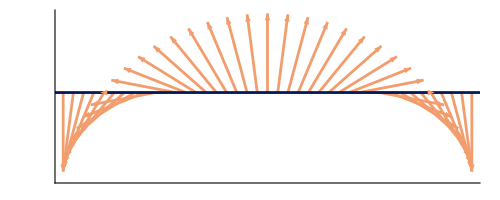

```mathematica
hpt1=Graphics[{cols[[1]],Thickness[.005],InfiniteLine[{{0,1},{1,1}}],cols[[5]],Table[Arrow[{{t,1},{t,1}+{Sin[t],Cos[t]}}],{t,-π,π,2π/40}]},PlotRange->{{-π,π},{-.1,2}},Axes->True,Ticks->None]
```

```mathematica
Export[NotebookDirectory[]<>"hpt1.pdf",hpt1]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/hpt1.pdf

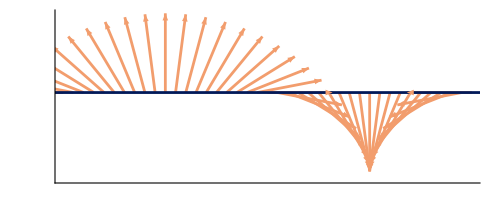

```mathematica
hpt2=Graphics[{cols[[1]],Thickness[.005],InfiniteLine[{{0,1},{1,1}}],cols[[5]],Table[Arrow[{{t,1},{t,1}+{Cos[t],-Sin[t]}}],{t,-π,π,2π/40}]},PlotRange->{{-π,π},{-.1,2}},Axes->True,Ticks->None]
```

```mathematica
Export[NotebookDirectory[]<>"hpt2.pdf",hpt2]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/hpt2.pdf

```mathematica
DSolve[{a'[t]==a[t]/t,b'[t]==b[t]/t},{a,b},t]
```

{{a→Function[{t},t C[1]],b→Function[{t},t C[2]]}}

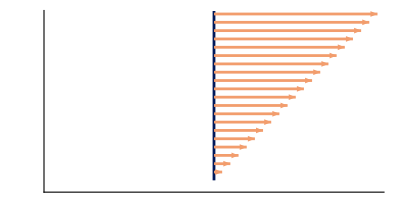

```mathematica
hpt3=Graphics[{cols[[1]],Thickness[.005],Line[{{0,4},{0,0}}],cols[[5]],Table[Arrow[{{0,t},{0,t}+{t,0}}],{t,0,2,.1}]},PlotRange->{{-2,2},{-.1,2}},Axes->True,Ticks->None]
```

```mathematica
Export[NotebookDirectory[]<>"hpt3.pdf",hpt3]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/hpt3.pdf

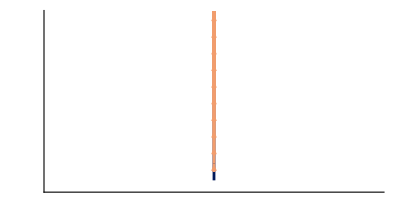

```mathematica
hpt4=Graphics[{cols[[1]],Thickness[.005],Line[{{0,4},{0,0}}],cols[[5]],Table[Arrow[{{0,t},{0,t}+{0,t}}],{t,0,2,.1}]},PlotRange->{{-2,2},{-.1,2}},Axes->True,Ticks->None]
```

```mathematica
Export[NotebookDirectory[]<>"hpt4.pdf",hpt4]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/hpt4.pdf

```mathematica
DSolve[θ'[t]==y[t]&&y'[t]==0,{θ,y},t]
```

{{y→Function[{t},C[1]],θ→Function[{t},t C[1]+C[2]]}}

In other words, the geodesic field on  is the field .

```mathematica
With[{dθ=2π/16,dy=.2},Manipulate[Graphics3D[{cols[[5]],Table[Arrow[Tube[{{r Cos[θ],r Sin[θ],y},{r Cos[θ],r Sin[θ],y} +{-r y Sin[θ],r y Cos[θ],0}}]],{θ,0,2π-dθ,dθ},{y,-1,1,dy}],Opacity[.3],cols[[4]],Cylinder[{{0,0,-1},{0,0,1}},1]},Lighting->"Neutral",Boxed->False,ViewPoint->Front],
{r,1,1.1}]]
```

```mathematica
circlegeodesicfield=With[{dθ=2π/16,dy=.2,r=1.0722},Show[Graphics3D[{cols[[5]],Table[Arrow[Tube[{{r Cos[θ],r Sin[θ],y},{r Cos[θ],r Sin[θ],y} +{-r y Sin[θ],r y Cos[θ],0}}]],{θ,0,2π-dθ,dθ},{y,-1,1,dy}],Opacity[.7],White,Cylinder[{{0,0,-1},{0,0,1}},1]}],ParametricPlot3D[{r Cos[θ],r Sin[θ],0},{θ,0,2π},PlotStyle->Directive[Thickness[.005],cols[[1]]]],Lighting->"Neutral",Boxed->False,ViewPoint->Front,ImageSize->600]]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"circlegeodesicfield.png",circlegeodesicfield,Background->None]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/circlegeodesicfield.png

Sphere

```mathematica
Clear[ϕ]
```

```mathematica
DSolve[{ϕ'[t]==y[t],θ'[t]==z[t],y'[t]==Sin[ϕ[t]]Cos[ϕ[t]] z[t]^2,z'[t]==-Cot[ϕ[t]]y[t]z[t]},{ϕ,θ,y,z},t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[{ϕ'[t]==y[t],θ'[t]==z[t],y'[t]==Cos[ϕ[t]] Sin[ϕ[t]] z[t]^2,z'[t]==-Cot[ϕ[t]] y[t] z[t]},{ϕ,θ,y,z},t]

```mathematica
f=NDSolve[{ϕ''[t]==Sin[ϕ[t]]Cos[ϕ[t]] θ'[t]^2,θ''[t]==-Cot[ϕ[t]]ϕ'[t]θ'[t],ϕ[0]==π/4,θ[0]==0,ϕ'[0]==0,θ'[0]==1},{ϕ,θ},{t,-.1,.1}][[1]]
```

{ϕ→InterpolatingFunction[…],θ→InterpolatingFunction[…]}

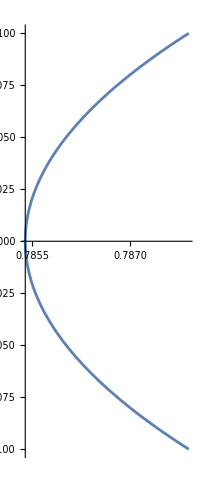

DSolve[{x''[t]==(2 x'[t] y'[t])/y[t],y''[t]==-(x'[t]^2-y'[t]^2)/y[t]},{x[t],y[t]},t]

```mathematica
ParametricPlot[{ϕ[t],θ[t]}/.f,{t,-.1,.1}]
```

```mathematica
DynamicModule[{vsol},
Manipulate[
vsol=NDSolve[{x''[t]==2/y[t] x'[t]y'[t],y''[t]==-1/y[t](x'[t]^2-y'[t]^2),x[0]==0,y[0]==1,x'[0]==Cos[θ],y'[0]==Sin[θ]},{x[t],y[t]},{t,-10,10}];
ParametricPlot[Evaluate[{x[t],y[t]}/.vsol],{t,-s,s},PlotStyle->Directive[Thickness[.01],Black],PlotRange->{{-2,2},{-.1,2}},Ticks->None],{s,0.01,10},{θ,0.,2π}]]
```

```mathematica
affgeo1=Module[{vsol},
ParallelTable[
vsol=NDSolve[{x''[t]==2/y[t] x'[t]y'[t],y''[t]==-1/y[t](x'[t]^2-y'[t]^2),x[0]==0,y[0]==1,x'[0]==Cos[θ],y'[0]==Sin[θ]},{x[t],y[t]},{t,-10,10}];
ParametricPlot[Evaluate[{x[t],y[t]}/.vsol],{t,-10,10},PlotStyle->Directive[Thickness[.005],Black],PlotRange->{{-2,2},{-.1,2}},Ticks->None],{θ,0.,2π-#,#}]]&[2π/100.];
```

```mathematica
Export[NotebookDirectory[]<>"affgeo.gif",affgeo1,"AnimationRepetitions"->Infinity,"DisplayDurations"->1/50]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/affgeo.gif

```mathematica
affgeo2=Module[{vsol},
Show[ParallelTable[
vsol=NDSolve[{x''[t]==2/y[t] x'[t]y'[t],y''[t]==-1/y[t](x'[t]^2-y'[t]^2),x[0]==0,y[0]==1,x'[0]==Cos[θ],y'[0]==Sin[θ]},{x[t],y[t]},{t,-10,10}];
ParametricPlot[Evaluate[{x[t],y[t]}/.vsol],{t,-10,10},PlotStyle->Directive[Thickness[.005],Black],PlotRange->{{-2,2},{-.1,2}},Ticks->None],{θ,0.,2π-#,#}]]]&[2π/16.];
```

```mathematica
Export[NotebookDirectory[]<>"affgeo.pdf",affgeo2]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/affgeo.pdf

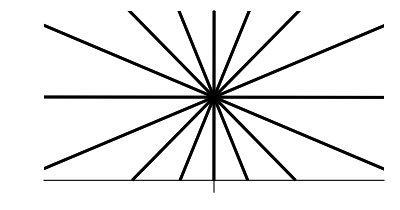

```mathematica
aff1par=ParametricPlot[Evaluate[Table[{(Sin[θ](E^(t Cos[θ])-1))/Cos[θ],E^(t Cos[θ])},{θ,0.001,2π+.001-#,#}]],{t,-10,10},PlotRange->{{-2,2},{-.1,2}},PlotStyle-> Directive[Thickness[.005],Black],Ticks->None]&[2π/16]
```

```mathematica
Export[NotebookDirectory[]<>"aff1par.pdf",aff1par]
```

/Users/shonk/Dropbox/Teaching/Math 670 Spring 2025/DG/figs/aff1par.pdf